```mathematica
Quit
```

```mathematica
vars={X1,X2,X3,𝒞,𝒜};
δvars={δx1,δx2,δx3,δC,δA};
pars={b1,b2,b3,bc,ba};
```

```mathematica
Clear[f]
```

```mathematica
f[eq_List]:=f[eq]=Module[{δeq,polys0,polys,ϕs},
δeq=Normal[Series[eq/.Join[{u->1+ϵ δu},Thread[vars->1+ϵ δvars],Thread[(#'&/@vars)-> (s ϵ δvars)]],{ϵ,0,1}]]/.ϵ->1;
polys0=(#[[1]]->Collect[Numerator[#[[2]]],s,Simplify]/Collect[Denominator[#[[2]]],s,Simplify]&/@Simplify/@Solve[δeq,δvars][[1]]/.δu->1);
polys=ComplexExpand[polys0/.{s->I ω}];
ϕs=#[[1]]->Factor[TrigToExp[ArcTan[(#[[2]])/(#[[1]])]&@(FullSimplify/@CoefficientList[#[[2]]/.I->j,j])]]&/@polys;
{TableForm[polys0],
TableForm[
{#[[1]],Union@Cases[#[[2]],Alternatives@@pars,∞],#[[2]]}&/@Table[
{i,FullSimplify@PowerExpand@ComplexExpand[FullSimplify[Factor[i.{1,-1}/.ϕs]//.{Log[x_]+Log[y_]->Log[ FullSimplify[x y]],Log[x_]-Log[y_]->Log[ FullSimplify[x/y]]}]]},
{i,Subsets[δvars,{2}]}],
TableDepth->1]}]
```

```mathematica
HPA={
X1'==b1 (u/X3- X1),
X2'==b2(𝒞 X1-X2),
X3'==b3(𝒜 X2-X3),
𝒞'==bc 𝒞(X1-1),
𝒜'==ba 𝒜(X2-1)};
```

```mathematica
f[HPA]
```

{δx1→(b1 b2 b3 s^2+b1 (b2+b3) s^3+b1 s^4)/(b1 b2 b3 ba bc+b1 b2 b3 (ba+bc) s+2 b1 b2 b3 s^2+(b2 b3+b1 (b2+b3)) s^3+(b1+b2+b3) s^4+s^5)
δx2→(b1 b2 b3 bc s+b1 b2 (b3+bc) s^2+b1 b2 s^3)/(b1 b2 b3 ba bc+b1 b2 b3 (ba+bc) s+2 b1 b2 b3 s^2+(b2 b3+b1 (b2+b3)) s^3+(b1+b2+b3) s^4+s^5)
δx3→(b1 b2 b3 ba bc+b1 b2 b3 (ba+bc) s+b1 b2 b3 s^2)/(b1 b2 b3 ba bc+b1 b2 b3 (ba+bc) s+2 b1 b2 b3 s^2+(b2 b3+b1 (b2+b3)) s^3+(b1+b2+b3) s^4+s^5)
δC→(b1 b2 b3 bc s+b1 (b2+b3) bc s^2+b1 bc s^3)/(b1 b2 b3 ba bc+b1 b2 b3 (ba+bc) s+2 b1 b2 b3 s^2+(b2 b3+b1 (b2+b3)) s^3+(b1+b2+b3) s^4+s^5)
δA→(b1 b2 b3 ba bc+b1 b2 ba (b3+bc) s+b1 b2 ba s^2)/(b1 b2 b3 ba bc+b1 b2 b3 (ba+bc) s+2 b1 b2 b3 s^2+(b2 b3+b1 (b2+b3)) s^3+(b1+b2+b3) s^4+s^5),{{δx1,δx2},{b2,bc},-1/2 Arg[((bc+ⅈ ω) (ⅈ b2+ω))/((bc-ⅈ ω) (-ⅈ b2+ω))]}
{{δx1,δx3},{b2,b3,ba,bc},-1/2 Arg[((b3-ⅈ ω) (ba+ⅈ ω) (bc+ⅈ ω) (ⅈ b2+ω))/((b2+ⅈ ω) (-ⅈ b3+ω) (ⅈ ba+ω) (ⅈ bc+ω))]}
{{δx1,δC},{},π/2}
{{δx1,δA},{b2,bc},1/2 Arg[((b2+ⅈ ω) (ⅈ bc+ω))/((bc+ⅈ ω) (ⅈ b2+ω))]}
{{δx2,δx3},{b3,ba},-1/2 Arg[((ba+ⅈ ω) (ⅈ b3+ω))/((ba-ⅈ ω) (-ⅈ b3+ω))]}
{{δx2,δC},{b2,bc},1/2 Arg[((bc+ⅈ ω) (ⅈ b2+ω))/((b2+ⅈ ω) (ⅈ bc+ω))]}
{{δx2,δA},{},π/2}
{{δx3,δC},{b2,b3,ba,bc},1/2 Arg[((b3-ⅈ ω) (ⅈ b2+ω) (-ⅈ ba+ω) (-ⅈ bc+ω))/((b3+ⅈ ω) (-ⅈ b2+ω) (ⅈ ba+ω) (ⅈ bc+ω))]}
{{δx3,δA},{b3,ba},1/2 Arg[((ba+ⅈ ω) (ⅈ b3+ω))/((b3+ⅈ ω) (ⅈ ba+ω))]}
{{δC,δA},{b2,bc},1/2 Arg[((b2+ⅈ ω) (ⅈ bc+ω))/((b2-ⅈ ω) (-ⅈ bc+ω))]}}

```mathematica
paraHPA={
b1->Log[2]/(4 min),b2->Log[2]/(20 min),b3->Log[2]/(80 min),
bc->Log[2]/(ac day),ba->Log[2]/(aa day),
ω->2π 1/(1 year),ω1->2π 1/(1 year),ω2->2π 1/(4 month) }/.{year->365 day,month->30 day,min->day/(60 24)};
units={year->1,month->1,day->1};
cond=Append[#,And@@#]&@({
4(2π (1-.25))^2≤ac^2(3/2 aa/ac-1/4(aa/ac)^2-1/4)≤4(2π (1+1/12))^2/.{ac->365/ac,aa->365/aa},
1.3<Abs[δx3/.f[HPA][[1,1]]/.s->I ω1]/Abs[δx3/.f[HPA][[1,1]]/.s->I ω2]<1.8,
-2.5<(6 Arg[(133225/(aa ac)+2 ⅈ (365/aa+365/ac) π)/(266450/(aa ac)+4 ⅈ (365/aa+365/ac) π-16 π^2)])/π<-0.5(*,
4<12/(2π)(Arg[(-ba (bc+ⅈ ω)+ⅈ bp ω)/(2 ba bc+2 ⅈ (ba+bc) ω-4 ω^2)])<8/.{ω->2π,ba->365/aa,bc->365/ac},
2<12/(2π)( (Arg[(-ba (bc+ⅈ ω)+ⅈ bc ω)/(2 ba bc+2 ⅈ (ba+bc) ω-4 ω^2)]-Arg[(ba bc+ⅈ (ba+bc) ω)/(2 ba bc+2 ⅈ (ba+bc) ω-4 ω^2)])/.{ω->2π,ba->365/aa,bc->365/ac})<6*)}/.paraHPA)/.units;
```

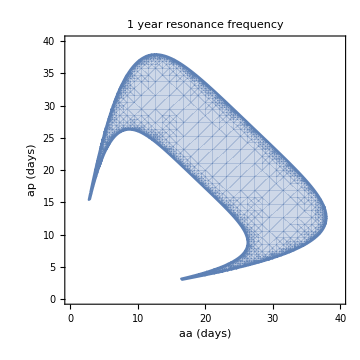
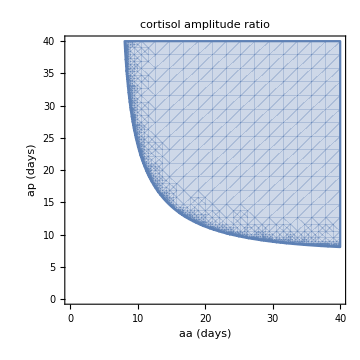
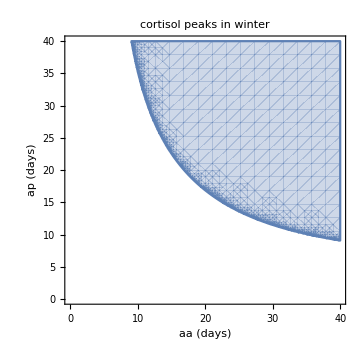
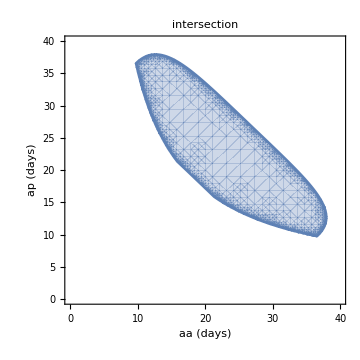

```mathematica
Row[Rs]
```

```mathematica
RegionPlot[Evaluate[cond],{aa,0,40/Log[2]},{ac,0,40/Log[2]},MaxRecursion->6,PlotPoints->50, FrameLabel->{"Adrenal cells half life time (days)","Corticotroph cells half life time (days)"},FrameStyle->18,PlotLegends->Placed[SwatchLegend[Style[#,14]&/@{"1 year resonance frequency","cortisol amplitude ratio","cortisol peaks in winter",(*"ACTH June",*)(*"ACTH - Cort phase shift",*)"intersection"},
LegendFunction->(Framed[#,Background->White]&)],{.78,.89}],]
```

-Graphics-